1.32066

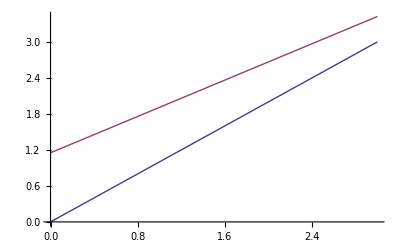

```mathematica
getLengthAnchor[P_, W_, segWidth_] := Module[{x},
Integrate[(((-(W-segWidth)Pi/P )*Sin[2Pi*x/P])^2+1)^(1/2),{ x, 0, P}]
]

W = 0.4;
P =1;
Lp = getLengthAnchor[P,W,0]

expr1 = Lq;
expr2 = P*(Lq + W/2 + Lp) / Lp ;
Plot[{expr1,expr2},{Lq,0,3}]
```

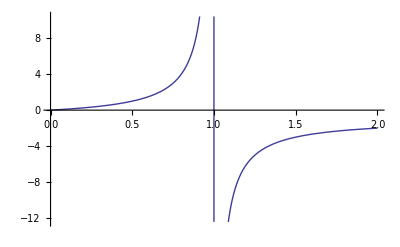

```mathematica
Plot[x/(1-x), {x, 0, 2}]
```

2.84132+Lc

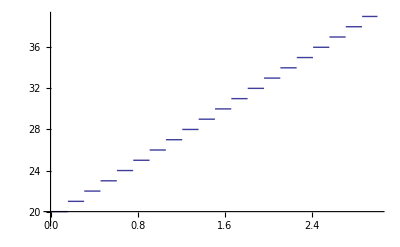

3.15868

```mathematica
L = Lc + W/2 + Lp + Lp
Plot[Ceiling[L/0.15],{Lc,0,3}]
40*0.15 - W/2 - Lp - Lp
```